```mathematica
OS="win";(*or linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\psi-nedm\\Analysis\\mNStar"]];
Print["(DescDir) Rawdata Directory: ",descDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\daq-tools-bkg-auto\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",ScrDir="C:\\Users\\Prajwal\\Dropbox\\Scratch"];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\Pictures"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\system"];
];
metaStructure={Real,Word,Real,Real,Real,Real,Real};
metaStructure2={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
```

Working Directory: C:\Users\Prajwal\Dropbox\nEDM\psi-nedm\Analysis\mNStar

(DescDir) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\daq-tools-bkg-auto\nstar_online

(AscDir) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\Prajwal\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\Prajwal\Dropbox\nEDM\Pictures

(SysDir) System Directory: C:\Users\Prajwal\Dropbox\nEDM\system

```mathematica
Print["Runs in the list: ",runNum1={13117,13118,13120,13121}];(*11159,11369*)
Print["Size: ",runn1=Dimensions[runNum1][[1]]];
iout={339.98,-339.96,170.03,-170.02};
ptdatib=ptdatif=ptcsdatib=ptcsdatif=Table[{0,{0,0}},{k,1,runn1}];
ftdatib=ftdatif=ftcsdatib=ftcsdatif=Table[{0,0},{k,1,runn1}];
ghg=7.590118;
gcs=3.5332539;
fcs={71.27114340170509,71.24680833579964,35.57571802511852,35.57557825681716};
errfcs=0.08923216141819122*10^(-3);
For[i=1,i≤runn1,i++,
metadat=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum1[[i]],10,6],"\\",IntegerString[runNum1[[i]],10,6],"_Meta3.edm"],metaStructure2];
ptdatib[[i]]={iout[[i]],{Sign[iout[[i]]]*metadat[[i]][[20]]/ghg,metadat[[i]][[21]]/ghg}};
ftdatib[[i]]={iout[[i]],Sign[iout[[i]]]*metadat[[i]][[20]]/ghg};
ptdatif[[i]]={iout[[i]],{Sign[iout[[i]]]*metadat[[i]][[20]],metadat[[i]][[21]]}};
ftdatif[[i]]={iout[[i]],Sign[iout[[i]]]*metadat[[i]][[20]]};
(*Cs*)
ptcsdatib[[i]]={iout[[i]],{Sign[iout[[i]]]*fcs[[i]]/gcs,errfcs/gcs}};
ftcsdatib[[i]]={iout[[i]],Sign[iout[[i]]]*fcs[[i]]/gcs};
ptcsdatif[[i]]={iout[[i]],{Sign[iout[[i]]]*fcs[[i]],errfcs}};
ftcsdatif[[i]]={iout[[i]],Sign[iout[[i]]]*fcs[[i]]};
];
ptdatib=AppendTo[ptdatib,{0,{0,4.57916158747466*10^(-7)}}];
ftdatib=AppendTo[ftdatib,{0,0}];
ptdatif=AppendTo[ptdatif,{0,{0,3.475637679*10^(-6)}}];
ftdatif=AppendTo[ftdatif,{0,0}];
(***)
ptcsdatib=AppendTo[ptcsdatib,{0,{0,4.57916158747466*10^(-7)}}];
ftcsdatib=AppendTo[ftcsdatib,{0,0}];
ptcsdatif=AppendTo[ptcsdatif,{0,{0,3.475637679*10^(-6)}}];
ftcsdatif=AppendTo[ftcsdatif,{0,0}];
(***)
nlm=NonlinearModelFit[ftdatib,aa+bb xx,{{aa,1},{bb,1}},xx]
nlm["ParameterTable"]
nlm2=NonlinearModelFit[ftdatif,aa+bb xx,{{aa,1},{bb,1}},xx]
nlm2["ParameterTable"]
nlmcs=NonlinearModelFit[ftcsdatib,aa+bb xx,{{aa,1},{bb,1}},xx]
nlmcs["ParameterTable"]
nlmcs2=NonlinearModelFit[ftcsdatif,aa+bb xx,{{aa,1},{bb,1}},xx]
nlmcs2["ParameterTable"]
```

Runs in the list: {13117,13118,13120,13121}

Size: 4

FittedModel[0.00159804+0.0599624 xx]

| Estimate | Standard Error | t-Statistic | P-Value
aa | 0.00159804 | 0.00512248 | 0.311966 | 0.775491
bb | 0.0599624 | 0.0000213076 | 2814.14 | 9.89544×10^-11

FittedModel[0.0121293+0.455122 xx]

| Estimate | Standard Error | t-Statistic | P-Value
aa | 0.0121293 | 0.0388802 | 0.311966 | 0.775491
bb | 0.455122 | 0.000161727 | 2814.14 | 9.89544×10^-11

FittedModel[0.00102958+0.0593024 xx]

| Estimate | Standard Error | t-Statistic | P-Value
aa | 0.00102958 | 0.00581545 | 0.177043 | 0.870753
bb | 0.0593024 | 0.0000241901 | 2451.52 | 1.4968×10^-10

FittedModel[0.00363778+0.20953 xx]

| Estimate | Standard Error | t-Statistic | P-Value
aa | 0.00363778 | 0.0205475 | 0.177043 | 0.870753
bb | 0.20953 | 0.0000854697 | 2451.52 | 1.4968×10^-10

```mathematica
metadat[[1]][[1]]
```

2017-10-12_10:55:34.435_UTC

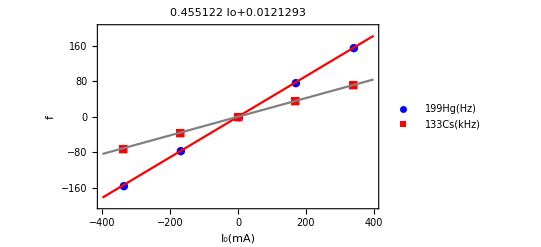

```mathematica
Show[{
EDAListPlot[ptdatif,ptcsdatif,PlotStyle->{Blue,Red,Gray,Green},PlotRange->{{-399,399},{-199,199}},Frame->True,FrameLabel->{"I_0(mA)","f"},PlotLegends->{"199Hg(Hz)","133Cs(kHz)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic,Large},PlotLabel->nlm2[Io]],
Plot[{nlm2[t],nlmcs2[t]},{t,-400,400},PlotStyle->{Red,Gray},PlotRange->Full,Frame->True,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000}]
}]
```

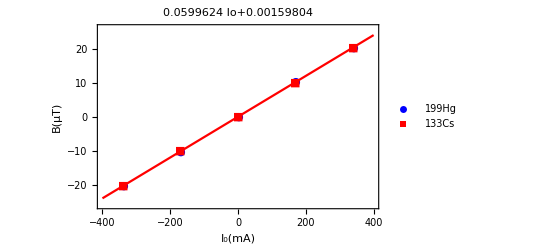

```mathematica
Show[{
EDAListPlot[ptdatib,ptcsdatib,PlotStyle->{Blue,Red,Gray,Green},PlotLegends->{"199Hg","133Cs"},PlotRange->{{-399,399},{-26,26}},Frame->True,FrameLabel->{"I_0(mA)","B(μT)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic, Large},PlotLabel->nlm[Io]],
Plot[{nlm[t]},{t,-400,400},PlotStyle->{Red,None,None},PlotRange->Full,Frame->True,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000}]
}]
```

## Cs-Hg Gradient

FittedModel[0.454763+0.528003 xx]

| Estimate | Standard Error | t-Statistic | P-Value
aa | 0.454763 | 0.974894 | 0.466474 | 0.672661
bb | 0.528003 | 0.00405519 | 130.204 | 9.9886×10^-7

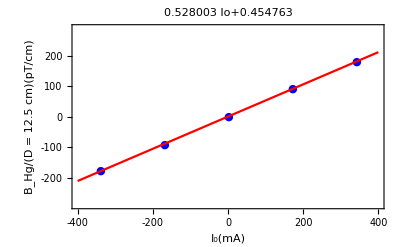

```mathematica
ptgdatib=Table[{0,{0,0}},{k,1,runn1+1}];
ftgdatib=Table[{0,0},{k,1,runn1+1}];
For[i=1,i≤runn1+1,i++,
ptgdatib[[i]]={ptdatib[[i]][[1]],{(ptdatib[[i]][[2]][[1]]-ptcsdatib[[i]][[2]][[1]])/12.5,ptdatib[[i]][[2]][[2]]+ptcsdatib[[i]][[2]][[2]]}*10000};
ftgdatib[[i]]={ftdatib[[i]][[1]],(ptdatib[[i]][[2]][[1]]-ptcsdatib[[i]][[2]][[1]])*10000/12.5};
]
nlmcsg=NonlinearModelFit[ftgdatib,aa+bb xx,{{aa,10},{bb,10}},xx]
nlmcsg["ParameterTable"]
Show[{
EDAListPlot[ptgdatib,PlotStyle->{Blue,Red,Gray,Green},PlotRange->{{-399,399},{-290,290}},Frame->True,FrameLabel->{"I_0(mA)","B_Hg/(D = 12.5  cm)(pT/cm)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic, Large},PlotLabel->nlmcsg[Io]],
Plot[{nlmcsg[t]},{t,-400,400},PlotStyle->{Red,None,None},PlotRange->Full,Frame->True,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000}]
}]
```

```mathematica
i=3
(ptdatib[[i]][[2]][[1]]-ptcsdatib[[i]][[2]][[1]])
```

3

0.113615

## After Highest Ramp

```mathematica
runNum2={13131};
i=1;
dathg=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum2[[i]],10,6],"\\",IntegerString[runNum2[[i]],10,6],"-0_PMT-readout3.edm"],{Word,Real}];
runn2=Dimensions[dathg][[1]]
ptdathg=Table[{0,0},{k,1,runn2}];
sttime=AbsoluteTime[dathg[[1]][[1]]];
For[j=1,j≤runn2,j++,
ptdathg[[j]]={AbsoluteTime[dathg[[j]][[1]]]-sttime,1+dathg[[j]][[2]]};
];
```

48203

```mathematica
k=0
st0=675;
st1=825;
st2=975;
nlm21=Interpolation[ptdathg[[st0+k*inter;;st1+k*inter]]];
nlm22=Interpolation[ptdathg[[st1+k*inter;;st2+k*inter]]];
1/((x/.FindMaximum[nlm22[x],{x,ptdathg[[st1+k*inter]][[1]]+.5}][[2]])-(x/.FindMaximum[nlm21[x],{x,ptdathg[[st0+k*inter]][[1]]+.5}][[2]]))
```

0

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.212896

{{10,19.4351},{154,18.5303},{298,18.9324},{442,17.8523},{586,17.363},{730,16.6984},{874,16.6942},{1018,16.3259},{1162,16.8285},{1306,16.2675}}

FittedModel[15.4824+4.07057 ⅇ^(-0.00127911 xx)]

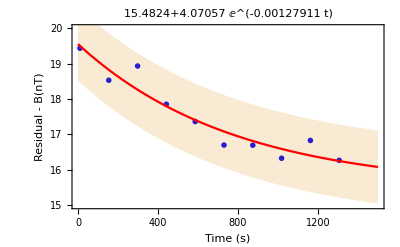

```mathematica
inter=4820;
st0=675;
st1=825;
st2=975;
int2=0;
freq=Table[0,{k,1,10}];
For[l=1,l≤10,l++,
k=l-1;
(*Print[EDAListPlot[ptdathg[[st0+k*inter;;st1+k*inter]],Joined->True,Frame->True,FrameLabel->{"Time (s)","PMT-Signal+1 (V)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic, Medium}]];
Print[EDAListPlot[ptdathg[[st1+k*inter;;st2+k*inter]],Joined->True,Frame->True,FrameLabel->{"Time (s)","PMT-Signal+1 (V)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic, Medium}]];*)
pos1=Flatten[Position[ptdathg[[st0+k*inter;;st1+k*inter,2]],Max[ptdathg[[st0+k*inter;;st1+k*inter,2]]]]][[1]];
pos2=Flatten[Position[ptdathg[[st1+k*inter;;st2+k*inter,2]],Max[ptdathg[[st2+k*inter;;st2+k*inter,2]]]]][[1]];
freq[[l]]=-1/(
7.590118*((ptdathg[[st0+k*inter;;st1+k*inter,1]][[pos1]])-(ptdathg[[st1+k*inter;;st2+k*inter,1]][[pos2]]))
);
]
ptfreq=Table[{10+(k-1)144,1000*freq[[k]]},{k,1,10}]
nlmexp=NonlinearModelFit[ptfreq,aa+bb Exp[cc xx],{{aa,0},{bb,1},{cc,-.1}},xx]
Show[{
EDAListPlot[ptfreq,PlotStyle->{Blue,Red,Gray,Green},PlotRange->{{0,1500},{15,20}},Frame->True,FrameLabel->{"Time (s)","Residual - B(nT)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic, Medium},PlotLabel->nlmexp[t]],
Plot[{nlmexp[t],nlmexp[t]-nlmexp["ParameterErrors"][[1]],nlmexp[t]+nlmexp["ParameterErrors"][[1]]},{t,0,1500},Filling->{{2->{3}}},PlotStyle->{Red,None,None},PlotRange->Full,Frame->True,FrameLabel->{"t_filling","N_Up+N_Down"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000}]
}]
```

```mathematica
Mean[Table[nlmexp[x],{x,32,180+32}]]
Mean[Table[nlmexp[x],{x,32,380+32}]]
```

18.9727

18.5772